```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

# Practica 1 Redes neuronales

```mathematica
Needs["PhysicalConstants`"]
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

BoltzmannConstant::shdw: Symbol BoltzmannConstant appears in multiple contexts {PhysicalConstants`,Notebook$$11$317803`}; definitions in context PhysicalConstants` may shadow or be shadowed by other definitions.

ElectronCharge::shdw: Symbol ElectronCharge appears in multiple contexts {PhysicalConstants`,Notebook$$11$317803`}; definitions in context PhysicalConstants` may shadow or be shadowed by other definitions.

```mathematica
Temperature = 273+20; (*K*)
```

## Ejercicio 1:

Usando la ecuacion de Nerst, determinar los potenciales de equilibrio para los siguientes  iones

Defino la ecuación de Nerst

```mathematica
BoltzConst = 8.6*10^-5; (* eVxK *)
```

```mathematica
VEquil[cOut_,cIn_]:=N[ BoltzConst*Temperature Log[cOut/cIn],2]
```

```mathematica
values=Association["K"->{20,430},"Na"->{440,50},"Cl"->{550,65}];
```

```mathematica
(VEquil[#[[1]],#[[2]]])&/@values
```

```mathematica
<|"K"->-0.07730879785949689,"Na"->0.05479939387795789,"Cl"->0.0538111103479215|>
```

<|K→-0.0773088,Na→0.0547994,Cl→0.0538111|>

## Ejercicio 2

Considerar una neurona esférica con un radio de 15 micrones y una capacitancia de 1.16F/cm^2. Que cantidad de iones de sodio deben ingresar a la neurona para cambiar el potencial de membrana en 100 mV? Comparar el cambio de concentración con la concentración de iones de sodio del problema anterior. Ayuda: usar como valor de la constante de Faraday: F=10^5 Coulombs/mol

```mathematica
Module[{r,C,V,F,A},
r = 15*^-3;
C=1*^-3/(1*^-2)^2;
V=100*^-3;
F=1*^5;
A = 4 *Pi*r^2;
n=N[C V A/F]
]
```

2.82743×10^-8

Este es el valor de concentracion necesario, se ve que es mucho menor que

## Ejercicio 3

Simular la dinámica de una neurona de Hogdkin-Huxley

```mathematica
Subscript[a, m][V_]:=0.1(V+40)/(1-Exp[-(V+40)/10])
Subscript[b, m][V_]:=4Exp[-(V+65)/18]
Subscript[a, h][V_]:=0.07Exp[-(V+65)/20]
Subscript[b, h][V_]:=1/(1+Exp[-(V+35)/10])
Subscript[a, n][V_]:=0.01(V+55)/(1-Exp[-(V+55)/10])
Subscript[b, n][V_]:=0.125Exp[-(V+65)/80]
```

```mathematica
Subscript[m, ∞][V_]:=Subscript[a, m][V]/(Subscript[a, m][V]+Subscript[b, m][V])
Subscript[h, ∞][V_]:=Subscript[a, h][V]/(Subscript[a, h][V]+Subscript[b, h][V])
Subscript[n, ∞][V_]:=Subscript[a, n][V]/(Subscript[a, n][V]+Subscript[b, n][V])
Subscript[tau, m][V_]:=1/(Subscript[a, m][V]+Subscript[b, m][V])
Subscript[tau, h][V_]:=1/(Subscript[a, h][V]+Subscript[b, h][V])
Subscript[tau, n][V_]:=1/(Subscript[a, n][V]+Subscript[b, n][V])
```

Inicializo los parametros externos

```mathematica
Cap = 1;
Subscript[V, Na]=50;
Subscript[V, k]=-77;
Subscript[V, l]=-54.5;
Subscript[g, Na]=120;
Subscript[g, k]=36;
Subscript[g, l]=0.3;
```

Resuelvo el sistema de ecuaciones diferenciales para diferentes valores de la corriente externa, variando en un rango de 2mA a 50mA.

```mathematica
freqData={};
plots = {};
Table[res=NDSolve[{V'[t]==1/Cap(Current-Subscript[g, Na] m[t]^3 h[t](V[t]-Subscript[V, Na])-Subscript[g, k] n[t]^4(V[t]-Subscript[V, k])-Subscript[g, l](V[t]-Subscript[V, l])),
m'[t]==(Subscript[m, ∞][V[t]]-m[t])/Subscript[tau, m][V[t]],
h'[t]==(Subscript[h, ∞][V[t]]-h[t])/Subscript[tau, h][V[t]],
n'[t]==(Subscript[n, ∞][V[t]]-n[t])/Subscript[tau, n][V[t]],
V[0]== -80,n[0]==0,h[0]==0,m[0]==0},{V,m,h,n},{t,0,200}];
results=res[[1,1]];
Vt = V/.results;
(*data = Abs[Fourier[Table[Vt[t],{t,20,200,0.01}]]];*)
peaks=FindPeaks[Table[Vt[t],{t,20,200,0.1}],10,0,0];
If[Length[peaks]>0,
frequency= 1/(Mean[Differences[First/@peaks]]*0.1),
frequency=0;
];
AppendTo[freqData,{Current,frequency}];
legend="Corriente = "<>ToString[Current]<>"mA, Frequ = "<>ToString[frequency];
If[Mod[(Current-2)/0.1,10]== 0,AppendTo[plots,Plot[Vt[t],{t,0,100},PlotRange->All,Epilog-> {Red,PointSize[0.02],Point[Map[{#[[1]]*0.1+20,#[[2]]}&,peaks]]},ImageSize->Medium,PlotLegends->Placed[legend,Top]]]]
(*p2 = ListLinePlot[data,PlotRange->{{2,20},{0,1000}}];*)
,{Current,2,50,0.1}];
```

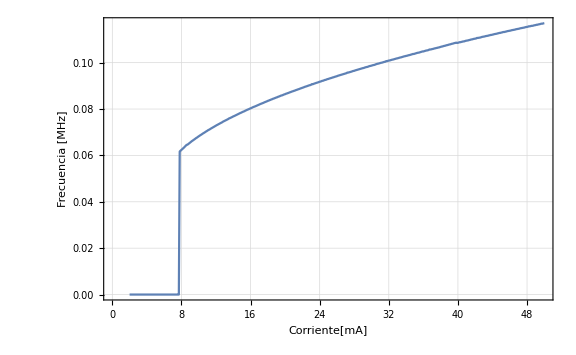

```mathematica
ListLinePlot[freqData,ImageSize->Large,
->True,GridLines->Automatic,Axes->True,FrameLabel->{"Corriente[mA]","Frecuencia [kHz]"}]
```

Se observa que alrededor de 7.6 mA comienzan a aparecer spikes con una determinada frecuencia y a medida que se continua aumentando la corriente externa dicha frecuencia aumenta.

## Ejercicio 4

Fijo la corriente a cero

```mathematica
Current = 0
```

Resuelvo el sistema de ecuaciones

```mathematica
res=NDSolve[{V'[t]==1/Cap(Current-Subscript[g, Na] m[t]^3 h[t](V[t]-Subscript[V, Na])-Subscript[g, k] n[t]^4(V[t]-Subscript[V, k])-Subscript[g, l](V[t]-Subscript[V, l])),
m'[t]==(Subscript[m, ∞][V[t]]-m[t])/Subscript[tau, m][V[t]],
h'[t]==(Subscript[h, ∞][V[t]]-h[t])/Subscript[tau, h][V[t]],
n'[t]==(Subscript[n, ∞][V[t]]-n[t])/Subscript[tau, n][V[t]],
V[0]== -80,n[0]==0,h[0]==0,m[0]==0},{V,m,h,n},{t,0,200}];
VRule = res[[1,1]];
mRule = res[[1,2]];
```

General::noinfo: Input expression InterpolatingFunction[{{0., 200.}}, <>] contains insufficient information to interpret the result.

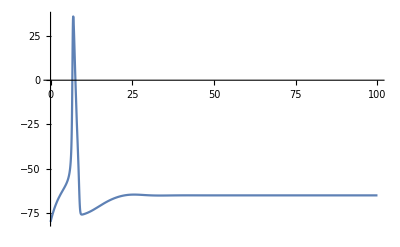

```mathematica
Plot[Evaluate[V[s]/.VRule],{s,0,100},PlotRange->All]
```

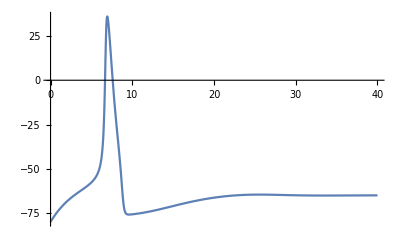

-Graphics-

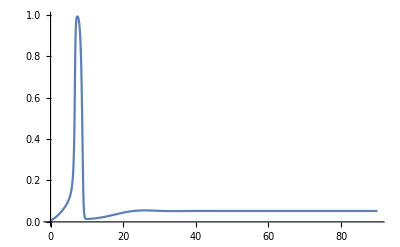

```mathematica
Plot[Evaluate[m[t]/.mRule],{t,0,90},PlotRange->All]
```

El sistema alcanza un punto fijo luego de 60ms (un poco antes en realidad, pero por seguridad tomo 60ms).

```mathematica
CurrentPulse[t_]:=If[t<60,0,If[t>(60+100),0,-4]]
```

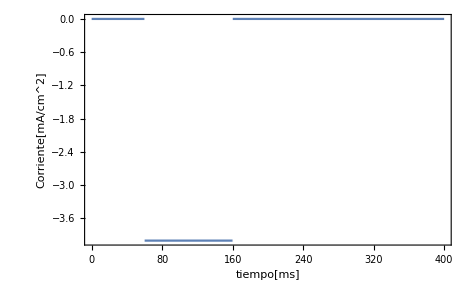

```mathematica
Plot[CurrentPulse[t],{t,0,400},Frame->True,FrameLabel->{"tiempo[ms]","Corriente[mA/cm^2]"}]
```

Ahora resuelvo el sitema con este pulso de corriente

```mathematica
res=NDSolve[{V'[t]==1/Cap(CurrentPulse[t]-Subscript[g, Na] m[t]^3 h[t](V[t]-Subscript[V, Na])-Subscript[g, k] n[t]^4(V[t]-Subscript[V, k])-Subscript[g, l](V[t]-Subscript[V, l])),
m'[t]==(Subscript[m, ∞][V[t]]-m[t])/Subscript[tau, m][V[t]],
h'[t]==(Subscript[h, ∞][V[t]]-h[t])/Subscript[tau, h][V[t]],
n'[t]==(Subscript[n, ∞][V[t]]-n[t])/Subscript[tau, n][V[t]],
V[0]== -80,n[0]==0,h[0]==0,m[0]==0},{V,m,h,n},{t,0,400}];
```

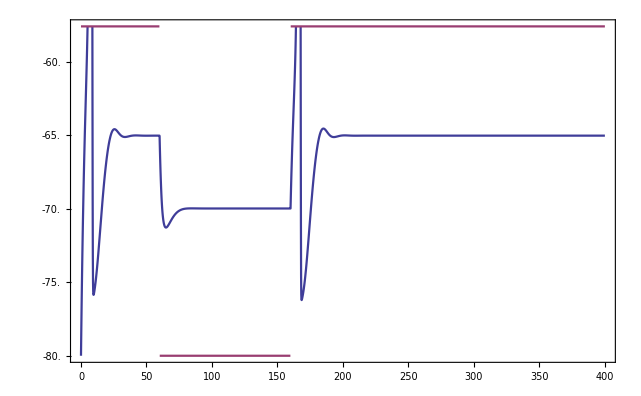

```mathematica
TwoAxisPlot[{Evaluate[V[t]/.res],Evaluate[CurrentPulse[t]]},{t,0,400}]
```

En el grafico de arriba se muestra como evoluciona el sistema luego de activar una corriente de 100 mA/cm^2 por 100 ms. 
Luego de que se apaga la corriente el sistema deja de emitir pulsos y regresa al punto fijo.

## Ejercicio 5

```mathematica
Current=1;
tau=1;
Subscript[tau, a]=1;
```

```mathematica
res=NDSolve[{tau V'[t]==Current-A[t]-V[t],Subscript[tau, a] A'[t]==-A[t],V[0]==0,A[0]==1},{V,A},{t,0,10}]
```

{{V→InterpolatingFunction[{{0., 10.}}, <>],A→InterpolatingFunction[{{0., 10.}}, <>]}}

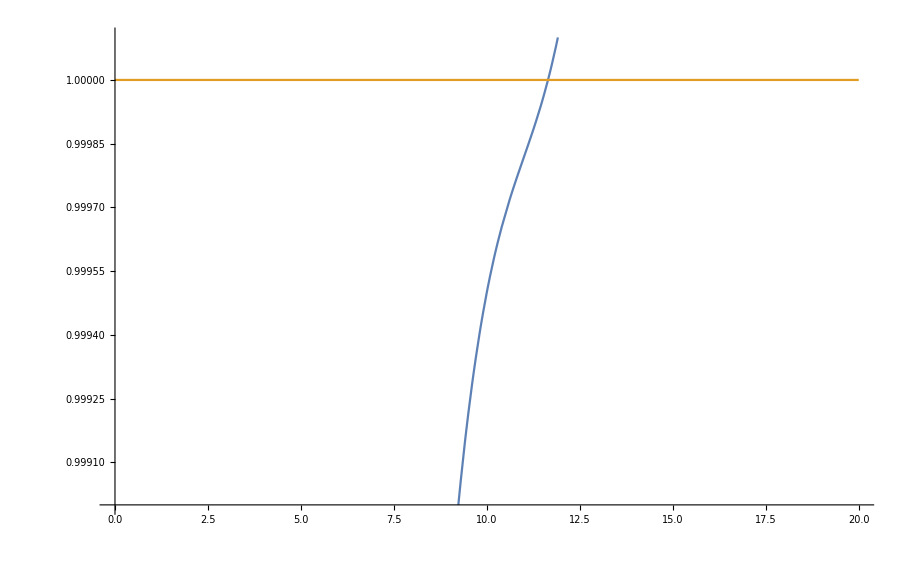

```mathematica
Plot[{Evaluate[V[t]/.res],1},{t,0,20},PlotRange->{0.999,1.0001}]
```

## Ejercicio 6

Calculo las nullclinas, obtengo dos sistemas de ecuaciones no lineales,

```mathematica
{a=0,Corriente=0.1,c=0.2};
```

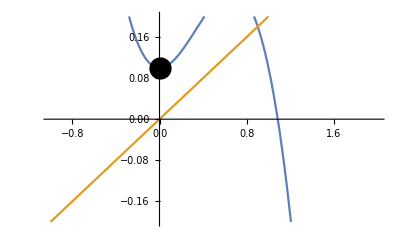

```mathematica
Plot[{x(a-x)(x-1)+Corriente,c x},{x,-1,2},PlotRange->{{-1,2},{-0.2,0.2}},Epilog->{PointSize[0.04],Point[{a,Corriente}]},PlotRange->All]
```

```mathematica
{a=0,Corriente=-0.048,c=0.2};
```

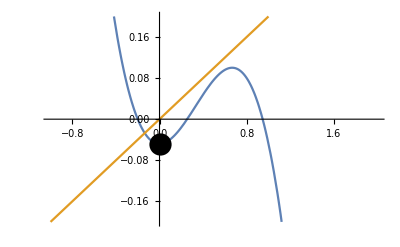

```mathematica
Plot[{x(a-x)(x-1)+Corriente,c x},{x,-1,2},PlotRange->{{-1,2},{-0.2,0.2}},Epilog->{PointSize[0.04],Point[{a,Corriente}]},PlotRange->All]
```

-Graphics-

{0.566,0.08,0.124}

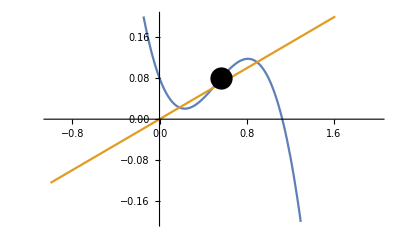

```mathematica
{a=0,Corriente=-0.048,c=0.2};
Plot[{x(a-x)(x-1)+Corriente,c x},{x,-1,2},PlotRange->{{-1,2},{-0.2,0.2}},Epilog->{PointSize[0.04],Point[{a,Corriente}]},PlotRange->All]
{a=0.566,Corriente=0.08,c=0.124}
Plot[{x(a-x)(x-1)+Corriente,c x},{x,-1,2},PlotRange->{{-1,2},{-0.2,0.2}},Epilog->{PointSize[0.04],Point[{a,Corriente}]},PlotRange->All]
```

En la figura de arriba aparecen graficadas la nulclina amarilla, la cual es lineal y la nulclina azul la cual es cubica, se puede ver como al variar la corriente aparecen diferentes puntos fijos.
Fijando a = 0.402 y c= b/γ=1 se obienen los siguientes puntos fijos en funcion de la corriente

```mathematica
Module[{a,c=0.1},
Manipulate[
f[x_]:=x(a-x)(x-1);
Plot[x/.Solve[f[x]+Corriente==c x,x],{Corriente,-0.1,0.1},AxesLabel->Automatic]
,{a,0,1}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Si el parametro c=b/γ es muy grande la curva se hace mas plana y solo aparece un punto fijo todo el tiempo.

Si definimos las funciones F[V,w] y G[V,w] como

```mathematica
f[V_]:=V(a-V)(V-2);
F[V_,w_]:=f[V]+ currnt - w
G[V_,w_]:=-γ w+b V
```

Podemos escribir la matriz jacobiana como

```mathematica
jacMatrix[V_,w_]:={{2 a (-1+V)+(4-3 V) V,-1},{b,-γ}}//FullSimplify;
jacMatrix//MatrixForm
```

SetDelayed::write: Tag List in {{(a-V) (-2+V)+(a-V) V-(-2+V) V,-1},{b,-γ}}[V_,w_] is Protected.

((a-V) (-2+V)+(a-V) V-(-2+V) V | -1
b | -γ)

Usando esta matriz podemos graficar el campo vectorial como

```mathematica
vectorField[V_,w_]:={(2 a (-1+V)+(4-3 V) V)*V,b V - γ w}
```

```mathematica
Manipulate[
vectorField[V_,w_]:={(2 a (-1+V)+(4-3 V) V)*V,b V - γ w};
VectorPlot[vectorField[x,y],{x,-2,2},{y,-2,2}],{a,0,1},{b,0,1},{γ,100,200}]
```